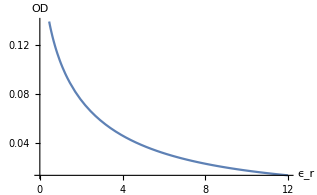

Inner conductor OD in inches should be

0.0161852

{{AWG→25.8687}}

Suggested American Wire Gauge diameter for ϵ_r = 10.6 is approximately

26

For this suggested gauge and given ϵ_r, impedance would be

50.2806Ω

```mathematica
ClearAll[s,ID, ohms,d,ϵr, sol, dia, OD, eq]
ID = .244; (* coax outer conductor ID, inches. symbol D is protected. *)
ohms = 50.; (* impedance of rest of microwave circuit *)
s = Solve[ohms== 377/(2π)(1/ϵr)^(1/2)Log[ID/d],d]/.Rule-> Equal; (* Solves eq. (1) in https://arxiv.org/pdf/1403.2909.pdf by Wollack, Chuss, et al. 
DOI: 10.1063/1.4869038 *)
sol = Part[s,1,1,2]; (* pick out RHS of solution *)
Plot[sol,{ϵr,0,12},AxesLabel->{ϵ_r,OD}] 
dia[ϵr_]:=sol; (* make sol into a function *)
ϵr = 10.6 ;(* Re[ϵ_r] for the lossy stycast & powder or Eccosorb mixture, based on material and frequency of operation *)
(* Eccosorb machinable stock MR-XXX is equivalent to castable resin CR-XXX:
http://www.eccosorb.com/Collateral/Documents/English-US/RFP-DS-MF%20092115.pdf *)
Print["Inner conductor OD in inches should be"]
od = dia[ϵr](* find OD of inner conductor needed to match ~50Ω. *)
eq = NSolve[od==.005*92^((36 - AWG)/39),AWG, Reals] (* conver OD to AWG number *)
Print["Suggested American Wire Gauge diameter for ϵ_r = ",ϵr," is approximately"]
awgsugg = Round[Part[eq,1,1,2]]
wiresugg = 0.005*92^((36-awgsugg)/39)//N; (* calc diameter based on suggested AWG *)
Z0calc= 377/(2π)(1/ϵr)^(1/2)Log[ID/wiresugg]; (* calc impedance based on AWG diameter *)
Print["For this suggested gauge and given ϵ_r, impedance would be"]
Print[Z0calc,"Ω"]
```